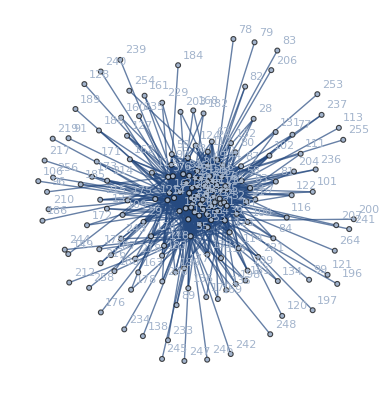

```mathematica
data = Import["C:\\Users\\brynbb\\Documents\\Wolfram Mathematica\\haggledata.txt"];
lines = StringSplit[data, "\n"];
lines = For[k=1,k≤Length[lines],k++,Sow[StringSplit[lines[[k]]]]]//Reap//Last//Last;
lines = For[k=1,k≤Length[lines],k++,Sow[{ToExpression[lines[[k]][[1]]],ToExpression[lines[[k]][[2]]],ToExpression[lines[[k]][[3]]]}]]//Reap//Last//Last;
lines = SortBy[lines,#[[3]]&];
n = Length[lines];
chop = 3*n/4;
train = lines[[;;chop]];
(*train = Select[lines, #[[3]] == "0"&];*)
test = lines[[chop+1;;]];
k = Length[test];
toPredict = For[i = 1,i≤ k,i++,Sow[{test[[i]][[1]],test[[i]][[2]]}]]//Reap//Last//Last;
g = Graph[UndirectedEdge @@@ train, VertexLabels->"Name"]


compare[predicted_,actual_]:=Intersection[predicted,actual]/Length[actual];
```

```mathematica
deleteduplicatepairs[pairs_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
Delete[pairs,todelete]];

dictionaryBackward[pairs_,nodes_]:=
Module[{n, new},
n = Length[pairs];
new = For[i=1,i≤n,i++, Sow[Sort[nodes[[pairs[[i]]]]]]]//Reap//Last//Last;
new];

(* brute force method for computing effective transition method for link prediction *)
modifiedEffectiveTransition[G_,k_]:=
Module[{M,spec,R,prediction, n, range,nodes,positions,cutoff},
nodes = VertexList[G];
Print[nodes];
n = VertexCount[G];
range = Range[n];
Print[Sort[range]];
M=N[AdjacencyMatrix[G]];
spec=Max[Abs[Eigenvalues[M,1]]];
R=RandomReal[{0,1},{n,n}];
For[i=1,i≤n,i++,For[j=i+1,j≤n,j++,R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=2,i≤n,i++,
For[j=1,j≤i-1,j++, R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=1,i≤n,i++,
R[[i]][[i]]=0;];
cutoff = TakeLargest[Flatten[R-10M],2*k][[2*k]];
positions = deleteduplicatepairs[Position[R-10M,_?(#≥ cutoff&)]];
Print[positions];
dictionaryBackward[positions,nodes]];
```

```mathematica
{time, predictedLinks} = Timing[modifiedEffectiveTransition[g, k]];
```

```mathematica
VertexList[g][[177]]
```

91

```mathematica
predictedLinks
```

True

1593

178

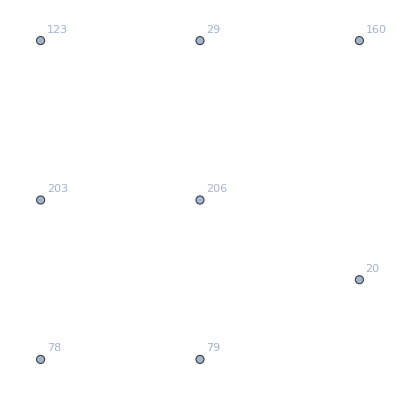

```mathematica
MemberQ[VertexList[g],29]
Length[EdgeList[g]]
Length[VertexList[g]]
Subgraph[g,{20,123,203,29,206,78,79,160}, VertexLabels->Automatic]
```

```mathematica
Intersection[test, predictedLinks]
```

{}

```mathematica
a= {{1,2},{4,5}}
b = {{1,2},{7,8}}
Intersection[a,b]
```

{{1,2},{4,5}}

{{1,2},{7,8}}

{{1,2}}

```mathematica
Intersection[toPredict,predictedLinks]
```

{}

```mathematica
a = Sort[{ToExpression[predictedLinks[[448]][[1]]],ToExpression[predictedLinks[[448]][[2]]]}]
a[[1]] == 91
```

{91,246}

True

```mathematica
Position[predictedLinks,{"246","91"}]
```

{{448}}

```mathematica
VertexList[g]
```

{20,35,21,47,43,61,55,56,15,24,8,9,3,25,12,19,5,7,14,23,13,45,2,27,17,10,46,11,1,22,16,40,4,6,48,18,26,123,203,76,29,31,206,28,42,78,79,160,161,32,120,209,77,237,112,168,121,162,127,118,37,178,131,243,80,236,258,163,113,214,169,215,216,33,264,253,49,242,30,138,233,58,179,133,122,187,234,170,39,180,181,132,65,114,115,34,38,36,125,116,59,41,88,44,111,53,52,81,204,51,54,87,50,63,117,90,102,57,89,182,100,124,101,128,198,212,60,210,221,256,82,196,197,171,183,184,172,173,185,254,241,174,175,244,245,246,186,83,134,247,135,235,248,229,217,106,136,109,239,188,240,177,176,218,219,149,207,199,220,96,200,62,189,99,137,255,91,84}

```mathematica
Position[VertexList[g],206]
```

{}

```mathematica
toPredict[[1]][[1]]=="10"
```

True

```mathematica
a = {"1","2"}
b = ToExpression[a]
```

{1,2}

{1,2}

```mathematica
a[[1]] == b[[1]]
```

False

```mathematica
b[[1]] == 1
```

True

```mathematica
prediction
```

prediction